Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 4 Contour Integration

Integrate z^2/(z^2-1) by Cauchy's formula counterclockwise around the circle.

1.  Abs[z + 1] = 1

```mathematica
Clear["Global`*"]
```

The formula for a circular plot in the given format needs to be recalled :
  ParametricPlot[{r Cos[t] + a, r Sin[t] + b}, {t, 0, 2 π}

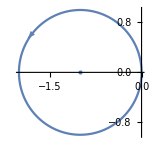

```mathematica
ParametricPlot[{1 Cos[z]-1, 1 Sin[z]+0},{z,0,2 π},ImageSize->150,Epilog->{{RGBColor[95/255,130/255,179/255],Arrowheads[0.1],Arrow[{{-1.805,0.6},{-1.85,0.55}}]},{RGBColor[95/255,130/255,179/255],Point[{-1,0}]}}]
```

This problem is covered in the s.m. As the s.m. points out, the first task is to find out where the problem function is not analytic. By inspection this is seen to be at the points z_0=-1 and 1. The point 1 is not a concern since it is not inside the domain, but the point -1 is. The non-analytic condition will occur when z_0=-1.

```mathematica
g[z_]=z^2/(z^2-1)
```

z^2/(-1+z^2)

```mathematica
Factor[g[z]]
```

z^2/((-1+z) (1+z))

Intending to use numbered line (1) on p.660
∮_C f[z]/(z-z_0)ⅆz=2 π ⅈ f[z_(0]),which is Cauchy's integral formula, the s.m. pulls out f[z] from

```mathematica
g[z_]=z^2/(z^2-1)==f[z]/(z-Subscript[z, 0])==f[z]/(z-(-1))
```

z^2/(-1+z^2)==f[z]/(z-z_0)==f[z]/(1+z)

and then operates on the first and last terms, multiplying by (1+z), yielding

```mathematica
f[z_]=z^2/(z-1)
```

Now moving to numbered line (1),

```mathematica
∮_C z^2/(z^2-1)ⅆz==∮_C f[z]/(z-Subscript[z, 0])ⅆz==∮_C (z^2/(z-1))/(z-(-1))ⅆz==2π ⅈ f[Subscript[z, 0]]==2 π ⅈ f[-1]==(2 π ⅈ)/-2==-π ⅈ
```

And the way to the text answer is neatly demonstrated.

3.  Abs[z + ⅈ] = 1.4

```mathematica
Clear["Global`*"]
```

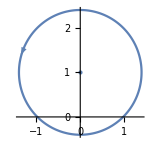

```mathematica
zirg=ParametricPlot[{1.4 Cos[z]+0, 1.4 Sin[z]+1},{z,0,2 π},ImageSize->150,Epilog->{{RGBColor[95/255,130/255,179/255],Arrowheads[0.1],Arrow[{{-1.305,1.5},{-1.35,1.4}}]},{RGBColor[95/255,130/255,179/255],Point[{0,1}]}}]
```

```mathematica
Solve[x^2+1==(1.4)^2,x]
```

{{x→-0.979796},{x→0.979796}}

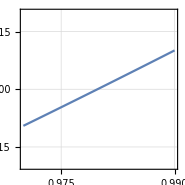

```mathematica
ContourPlot[x^2+(y-1)^2==(1.4)^2,{x,0.97,0.99},{y,-0.02,0.02},GridLines->Automatic,ImageSize->185]
```

Whereas in the parametric plot it looked like the unanalytic points might be at 1 and -1 exactly, a closer looks shows that they are not exactly on the curve. In fact they are outside the domain, which means that Cauchy’s theorem has a chance to take effect.

```mathematica
f[z_]=z^2/(z^2-1)
```

z^2/(-1+z^2)

```mathematica
f[x_,y_]=f[z]/.z->(x+ⅈ y)
```

(x+ⅈ y)^2/(-1+(x+ⅈ y)^2)

```mathematica
ComplexExpand[%]
```

-x^2/(4 x^2 y^2+(-1+x^2-y^2)^2)+x^4/(4 x^2 y^2+(-1+x^2-y^2)^2)-(2 ⅈ x y)/(4 x^2 y^2+(-1+x^2-y^2)^2)+y^2/(4 x^2 y^2+(-1+x^2-y^2)^2)+(2 x^2 y^2)/(4 x^2 y^2+(-1+x^2-y^2)^2)+y^4/(4 x^2 y^2+(-1+x^2-y^2)^2)

```mathematica
u[x_,y_]=-x^2/(4 x^2 y^2+(-1+x^2-y^2)^2)+x^4/(4 x^2 y^2+(-1+x^2-y^2)^2)+y^2/(4 x^2 y^2+(-1+x^2-y^2)^2)+(2 x^2 y^2)/(4 x^2 y^2+(-1+x^2-y^2)^2)+y^4/(4 x^2 y^2+(-1+x^2-y^2)^2)
```

-x^2/(4 x^2 y^2+(-1+x^2-y^2)^2)+x^4/(4 x^2 y^2+(-1+x^2-y^2)^2)+y^2/(4 x^2 y^2+(-1+x^2-y^2)^2)+(2 x^2 y^2)/(4 x^2 y^2+(-1+x^2-y^2)^2)+y^4/(4 x^2 y^2+(-1+x^2-y^2)^2)

```mathematica
v[x_,y_]=-(2  x y)/(4 x^2 y^2+(-1+x^2-y^2)^2)
```

-(2 x y)/(4 x^2 y^2+(-1+x^2-y^2)^2)

```mathematica
D[u[x,y],x];
```

```mathematica
FullSimplify[%]
```

(-2 x (-1+x^2)^2+4 x (1+x^2) y^2+6 x y^4)/((x^4+2 x^2 (-1+y^2)+(1+y^2)^2)^2)

```mathematica
D[v[x,y],y];
```

```mathematica
FullSimplify[%]
```

(-2 x (-1+x^2)^2+4 x (1+x^2) y^2+6 x y^4)/((x^4+2 x^2 (-1+y^2)+(1+y^2)^2)^2)

```mathematica
-D[u[x,y],y];
```

```mathematica
FullSimplify[%]
```

((-1+x) y)/(((-1+x)^2+y^2)^2)-((1+x) y)/(((1+x)^2+y^2)^2)

```mathematica
D[v[x,y],x];
```

```mathematica
FullSimplify[%]
```

((-1+x) y)/(((-1+x)^2+y^2)^2)-((1+x) y)/(((1+x)^2+y^2)^2)

Cyan and pink cells match. The function proves to be analytic for all real x and y. It meets the requirements of Cauchy’s theorem, and therefore the contour integral equals zero.

5 - 8 Integrate the given function around the unit circle.

5.  Cos[3 z]/(6 z)

```mathematica
Clear["Global`*"]
```

This problem admits use of Cauchy’s Integral Formula. It is first split up,

```mathematica
f[z_]=Cos[3 z]/6
```

1/6 Cos[3 z]

The point of difficulty is z_0=0 .

```mathematica
f[0]
```

1/6

And to put it in the form of Cauchy’s Integral Formula, numbered line (1) on p. 660,
 ∮_C f[z]/(z-z_0)ⅆz =2πⅈf[z_0]

Checking the Cauchy conditions. Is the unit circle, D, simply connected? Yes. Is f[z] analytic in D? The cosine function is analytic and holomorphic, and multiplying by real 1/6 will not disturb this. Nevertheless I will check it.

```mathematica
f[x_,y_]=f[z]/.z->(x+ⅈ y)
```

1/6 Cos[3 (x+ⅈ y)]

```mathematica
ComplexExpand[%]
```

1/6 Cos[3 x] Cosh[3 y]-1/6 ⅈ Sin[3 x] Sinh[3 y]

```mathematica
u[x_,y_]=1/6 Cos[3 x] Cosh[3 y]
```

1/6 Cos[3 x] Cosh[3 y]

```mathematica
v[x_,y_]=-1/6  Sin[3 x] Sinh[3 y]
```

-1/6 Sin[3 x] Sinh[3 y]

```mathematica
D[u[x,y],x]
```

-1/2 Cosh[3 y] Sin[3 x]

```mathematica
D[v[x,y],y]
```

-1/2 Cosh[3 y] Sin[3 x]

```mathematica
-D[u[x,y],y]
```

-1/2 Cos[3 x] Sinh[3 y]

```mathematica
D[v[x,y],x]
```

-1/2 Cos[3 x] Sinh[3 y]

The function f[z] is analytic. The preliminaries having been taken care of, I can now write the rhs of the Cauchy Integral Formula,

```mathematica
2πⅈ f[0]
```

πⅈ/3

7.  z^3/(2 z-ⅈ)

```mathematica
Clear["Global`*"]
```

This problem also invites use of Cauchy’s Integral Formula. First splitting it up,

```mathematica
f[z_]=z^3/2
```

z^3/2

The point of difficulty is z_0=1/2 ⅈ

```mathematica
f[ⅈ/2]
```

-ⅈ/16

Checking analyticity,

```mathematica
f[x_,y_]=f[z]/.z->(x+ⅈ y)
```

1/2 (x+ⅈ y)^3

```mathematica
ComplexExpand[%]
```

x^3/2-(3 x y^2)/2+ⅈ ((3 x^2 y)/2-y^3/2)

```mathematica
u[x_,y_]=x^3/2-(3 x y^2)/2
```

x^3/2-(3 x y^2)/2

```mathematica
v[x_,y_]=(3 x^2 y)/2-y^3/2
```

(3 x^2 y)/2-y^3/2

```mathematica
D[u[x,y],x]
```

(3 x^2)/2-(3 y^2)/2

```mathematica
D[v[x,y],y]
```

(3 x^2)/2-(3 y^2)/2

```mathematica
-D[u[x,y],y]
```

3 x y

```mathematica
D[v[x,y],x]
```

3 x y

Retrieving the rhs of the Cauchy Integral Formula,

```mathematica
2π ⅈ f[ⅈ/2]
```

π/8

11 - 19 Further Contour Integrals
Integrate counterclockwise or as indicated.

11.  ∮_C ⅆz/(z^2+4),  C: 4 x^2+(y-2)^2==4

```mathematica
Clear["Global`*"]
```

I think I should have a look at the domain.

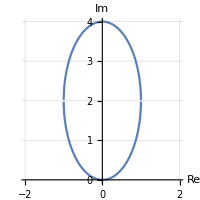

```mathematica
Plot[y/.Solve[x^2+ ((y-2)/2)^2==1],{x,-2,2},AspectRatio->Automatic,ImageSize->200,AxesLabel->{"Re","Im"},GridLines->Automatic]
```

```mathematica
g[z_]=1/(z^2+4)
```

1/(4+z^2)

```mathematica
Solve[z^2+4==0,z]
```

{{z→-2 ⅈ},{z→2 ⅈ}}

z_0=2 ⅈ lies in the domain, whereas z_0=-2 ⅈ does not. Using Cauchy’s Integral Formula, 
g[z]=1/(z^2+4)=f[z]/(z-z_0)=f[z]/(z-2ⅈ)

```mathematica
Solve[1/(z^2+4)==f[z]/(z-2ⅈ),f[z]]
```

{{f[z]→1/(2 ⅈ+z)}}

and, initializing

```mathematica
f[z_]=1/(2 ⅈ+z)
```

1/(2 ⅈ+z)

so that I can calculate f[z_0],

```mathematica
f[2 ⅈ ]
```

-ⅈ/4

resulting in the rhs of Cauchy’s Integral Formula,

```mathematica
2 π ⅈ(-ⅈ/4)
```

π/2

Matching the answer in the text. All very well, but I didn’t yet check the analyticity of g[x].

```mathematica
f[x_,y_]=g[z]/.z->(x+ⅈ y)
```

1/(4+(x+ⅈ y)^2)

```mathematica
ComplexExpand[%]
```

4/(4 x^2 y^2+(4+x^2-y^2)^2)+x^2/(4 x^2 y^2+(4+x^2-y^2)^2)-(2 ⅈ x y)/(4 x^2 y^2+(4+x^2-y^2)^2)-y^2/(4 x^2 y^2+(4+x^2-y^2)^2)

```mathematica
u[x_,y_]=4/(4 x^2 y^2+(4+x^2-y^2)^2)+x^2/(4 x^2 y^2+(4+x^2-y^2)^2)-y^2/(4 x^2 y^2+(4+x^2-y^2)^2)
```

4/(4 x^2 y^2+(4+x^2-y^2)^2)+x^2/(4 x^2 y^2+(4+x^2-y^2)^2)-y^2/(4 x^2 y^2+(4+x^2-y^2)^2)

```mathematica
v[x_,y_]=-(2 x y)/(4 x^2 y^2+(4+x^2-y^2)^2)
```

-(2 x y)/(4 x^2 y^2+(4+x^2-y^2)^2)

```mathematica
D[u[x,y],x];
```

```mathematica
FullSimplify[%]
```

(-2 x (4+x^2)^2+4 x (-4+x^2) y^2+6 x y^4)/((x^4+(-4+y^2)^2+2 x^2 (4+y^2))^2)

```mathematica
D[v[x,y],y];
```

```mathematica
FullSimplify[%]
```

(-2 x (4+x^2)^2+4 x (-4+x^2) y^2+6 x y^4)/((x^4+(-4+y^2)^2+2 x^2 (4+y^2))^2)

```mathematica
-D[v[x,y],x];
```

```mathematica
FullSimplify[%]
```

(2 y (-3 x^4+(-4+y^2)^2-2 x^2 (4+y^2)))/((x^4+(-4+y^2)^2+2 x^2 (4+y^2))^2)

```mathematica
D[u[x,y],y];
```

```mathematica
FullSimplify[%]
```

(2 y (-3 x^4+(-4+y^2)^2-2 x^2 (4+y^2)))/((x^4+(-4+y^2)^2+2 x^2 (4+y^2))^2)

Thus showing that g[x] is indeed analytic, and that the green cell above is valid.

13.  ∮_C (z+2)/(z-2)ⅆz, C: Abs[z-1]==2

```mathematica
Clear["Global`*"]
```

Again, I will first plot the domain.

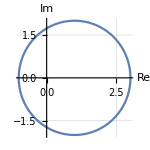

```mathematica
ParametricPlot[{2 Cos[t] + 1, 2 Sin[t] }, {t, 0, 2 π},ImageSize->150,AxesLabel->{"Re","Im"},GridLines->Automatic]
```

```mathematica
g[z_]=(z+2)/(z-2)
```

(2+z)/(-2+z)

I will adopt the procedure again of assuming that g[x] is analytic in the domain, though I may check it later. The problem point is z_0=(2,0). It seems straightforward to assign

```mathematica
f[z_]=z+2
```

2+z

and

```mathematica
f[2]
```

4

So that assembling the Cauchy Integral Formula, I get

```mathematica
2 π ⅈ (4)
```

8 ⅈ π

which matches the answer in the text. As for the question of analyticity,

```mathematica
f[x_,y_]=g[z]/.z->(x+ⅈ y)
```

(2+x+ⅈ y)/(-2+x+ⅈ y)

```mathematica
ComplexExpand[%]
```

-4/((-2+x)^2+y^2)+x^2/((-2+x)^2+y^2)-(4 ⅈ y)/((-2+x)^2+y^2)+y^2/((-2+x)^2+y^2)

```mathematica
u[x_,y_]=-4/((-2+x)^2+y^2)+x^2/((-2+x)^2+y^2)+y^2/((-2+x)^2+y^2)
```

-4/((-2+x)^2+y^2)+x^2/((-2+x)^2+y^2)+y^2/((-2+x)^2+y^2)

```mathematica
v[x_,y_]=-(4 y)/((-2+x)^2+y^2)
```

-(4 y)/((-2+x)^2+y^2)

```mathematica
D[u[x,y],x];
```

```mathematica
FullSimplify[%]
```

(-4 (-2+x)^2+4 y^2)/(((-2+x)^2+y^2)^2)

```mathematica
D[v[x,y],y];
```

```mathematica
FullSimplify[%]
```

(-4 (-2+x)^2+4 y^2)/(((-2+x)^2+y^2)^2)

```mathematica
-D[v[x,y],x];
```

```mathematica
FullSimplify[%]
```

-(8 (-2+x) y)/(((-2+x)^2+y^2)^2)

```mathematica
D[u[x,y],y];
```

```mathematica
FullSimplify[%]
```

-(8 (-2+x) y)/(((-2+x)^2+y^2)^2)

Demonstrating that the function g[z] is analytic.

15.  ∮_C Cosh[z^2-π ⅈ]/(z-π ⅈ)ⅆz , C: the boundary of the square with vertices ±2,±2,±4ⅈ

```mathematica
Clear["Global`*"]
```

Something is wrong with the statement of the problem. The domain square is messed up, I will assume it is the square with corners ±2+0ⅈ, and ±2+4 ⅈ, as so:

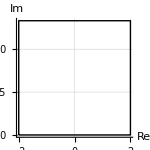

```mathematica
Graphics[Line[{{-2,0},{2,0},{2,4},{-2,4},{-2,0}}],ImageSize->150,Axes->True,AxesLabel->{"Re","Im"},GridLines->Automatic]
```

```mathematica
g[z_]=Cosh[z^2-π ⅈ]/(z-π ⅈ)
```

-Cosh[z^2]/(-ⅈ π+z)

It looks like the problem point is z_0= (0+π ⅈ), which does belong to the domain pictured. This would mean that

```mathematica
f[z_]=-Cosh[z^2]
```

-Cosh[z^2]

and f[z_0] would be

```mathematica
f[π ⅈ]
```

-Cosh[π^2]

So the rhs of the Cauchy Integral Formula would just be

```mathematica
2 π ⅈ (-Cosh[π^2])
```

-2 ⅈ π Cosh[π^2]

```mathematica
N[%]
```

0.-60738.6 ⅈ

Both green cells above match the text answer. So this one is done, except that the analyticity of g[z] has not yet been checked. (And by the way, the assumption about the vertices of the domain seems to have been confirmed by the answer.)

```mathematica
f[x_,y_]=g[z]/.z->(x+y ⅈ)
```

-Cosh[(x+ⅈ y)^2]/(-ⅈ π+x+ⅈ y)

```mathematica
ComplexExpand[%]
```

-(x Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)+(π Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)-(y Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)+ⅈ (-(π Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)+(y Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)-(x Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2))

```mathematica
u[x_,y_]=-(x Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)+(π Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)-(y Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)
```

-(x Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)+(π Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)-(y Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)

```mathematica
v[x_,y_]=-(π Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)+(y Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)-(x Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)
```

-(π Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)+(y Cos[2 x y] Cosh[x^2-y^2])/(x^2+(-π+y)^2)-(x Sin[2 x y] Sinh[x^2-y^2])/(x^2+(-π+y)^2)

```mathematica
D[u[x,y],x];
```

```mathematica
FullSimplify[%]
```

1/((x^2+(π-y)^2)^2)(Cosh[(x-y) (x+y)] (-(π-x-y) (π+x-y) Cos[2 x y]+2 π x (x^2+(π-y)^2) Sin[2 x y])+2 (-(x^2+(π-y)^2) (x^2-π y+y^2) Cos[2 x y]+x (-π+y) Sin[2 x y]) Sinh[(x-y) (x+y)])

```mathematica
D[v[x,y],y];
```

```mathematica
FullSimplify[%]
```

1/((x^2+(π-y)^2)^2)(Cosh[(x-y) (x+y)] (-(π-x-y) (π+x-y) Cos[2 x y]+2 π x (x^2+(π-y)^2) Sin[2 x y])+2 (-(x^2+(π-y)^2) (x^2-π y+y^2) Cos[2 x y]+x (-π+y) Sin[2 x y]) Sinh[(x-y) (x+y)])

```mathematica
-D[v[x,y],x];
```

```mathematica
FullSimplify[%]
```

1/((x^2+(π-y)^2)^2)(2 Cosh[(x-y) (x+y)] (x (-π+y) Cos[2 x y]+(x^2+(π-y)^2) (x^2-π y+y^2) Sin[2 x y])+(2 π x (x^2+(π-y)^2) Cos[2 x y]+(π-x-y) (π+x-y) Sin[2 x y]) Sinh[(x-y) (x+y)])

```mathematica
D[u[x,y],y];
```

```mathematica
FullSimplify[%]
```

1/((x^2+(π-y)^2)^2)(2 Cosh[(x-y) (x+y)] (x (-π+y) Cos[2 x y]+(x^2+(π-y)^2) (x^2-π y+y^2) Sin[2 x y])+(2 π x (x^2+(π-y)^2) Cos[2 x y]+(π-x-y) (π+x-y) Sin[2 x y]) Sinh[(x-y) (x+y)])

Confirming the analyticity of g[z].

17.   ∮_C Log[z+1]/(z^2+1)ⅆz , C: Abs[z-ⅈ]==1.4

```mathematica
Clear["Global`*"]
```

First to examine the domain.

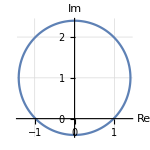

```mathematica
ParametricPlot[{1.4 Cos[t] , 1.4 Sin[t]+1 }, {t, 0, 2 π},ImageSize->150,AxesLabel->{"Re","Im"},GridLines->Automatic]
```

```mathematica
g[z_]=Log[z+1]/(z^2+1)
```

Log[1+z]/(1+z^2)

It is apparent that the obstacle point will be z_0=0+ⅈ, which is included in the domain. Suppose I make

```mathematica
f[z_]=Log[z+1]/(z+ⅈ)
```

Log[1+z]/(ⅈ+z)

then

```mathematica
f[z] 1/(z-ⅈ)
```

Log[1+z]/((-ⅈ+z) (ⅈ+z))

which is just what I want, because it will fit directly into the Cauchy Integral Formula.

```mathematica
f[z]2π ⅈ
```

(2 ⅈ π Log[1+z])/(ⅈ+z)

```mathematica
f[ⅈ]2π ⅈ
```

π Log[1+ⅈ]

```mathematica
N[%]
```

1.08879+2.4674 ⅈ

The green cells above match the text answer. All that remains is to check analyticity of g[z]. This turns out to be more difficult than expected. So I’m going to weasle out on this one. According to Wikipedia, the log function is analytic on any open set in its domain, and polynomials, like z^2+1, are analytic. According to http://kisonecat.com/teaching/2011/math660/lecture02.pdf, the quotient of analytic functions is analytic, as long as the denominator is non-zero.

19.  ∮_C Exp[z^2]/(z^2(z-1-ⅈ))ⅆz, C: consists of Abs[z]==2 counterclockwise and Abs[z]==1 clockwise.

This problem is included in the s.m. First I will make a sketch.

```mathematica
Clear["Global`*"]
```

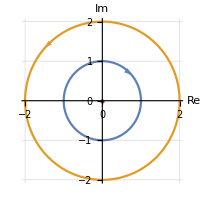

```mathematica
ParametricPlot[{{1 Cos[t] , 1 Sin[t] },{2 Cos[t] , 2 Sin[t] }}, {t, 0, 2 π},ImageSize->200,AxesLabel->{"Re","Im"},GridLines->Automatic,Epilog->{{RGBColor[95/255,130/255,179/255],Arrowheads[0.08],Arrow[{{0.708,0.687},{0.74,0.66}}]},{Red,Point[{0,0}]},{RGBColor[223/255,155/255,52/255],Arrowheads[0.08],Arrow[{{-1.26,1.55},{-1.48,1.35}}]}}]
```

I see two obstacle points, one at 0+0ⅈ, and another at 1+ⅈ. Only the second problem point is in the domain.
So I will just write

```mathematica
g[z]=Exp[z^2]/(z^2(z-1-ⅈ))
```

(ⅇ^(z^2))/(((-1-ⅈ)+z) z^2)

and, leaving in the denominator of the original g[z] only what seems to handle the problem point, I will have

```mathematica
f[z_]=Exp[z^2]/z^2
```

(ⅇ^(z^2))/z^2

I need to have the problem point ready to hand

```mathematica
Subscript[z, 0]=1+ⅈ
```

1+ⅈ

and also the value of f evaluated at the problem point

```mathematica
f[Subscript[z, 0]]
```

-1/2 ⅈ ⅇ^(2 ⅈ)

then to assemble the rhs of the Cauchy Integral Formula

```mathematica
2 π ⅈ(f[Subscript[z, 0]])
```

ⅇ^(2 ⅈ) π

The above cell matches the text answer. The analyticity of g[z] is vouched for in the same way as the last problem, Wikipedia specifically mentioning the exponential function as being analytic.